```mathematica
DateString[]
$Version
```

Thu 11 Jan 2018 02:50:20

## At Day 3

[1] S. Wolfram, An Elementary Introduction to the Wolfram Language, 2nd ed. Wolfram Media, Inc., 2017.

-Graphics-

### 18 Geocomputation *

18 Geocomputation

Picky exercises: 3, 5, 6, 10, 11, 12, +4

Tweet-a-Program:

```mathematica
GeoGraphics[Text[Style["Hello!",150]],GeoRange->"World"]
```

### 19 Dates and Times *

19 Dates and Times

Picky exercises: 3, 7, +1,

### 20 Options

20 Options

Picky exercises: 4, 7, 9, 10, +3, +8

Tweet-a-Program

```mathematica
Plot[Sin[x],{x,0,2π},ColorFunctionScaling->False, ColorFunction->(ColorData["TemperatureMap"][Abs@#2]&)]
```

### 21 Graphs and Networks

21 Graphs and Networks

Picky exercises: 9, +2, +3, +7

### 22 Machine Learning *

22 Machine Learning

scikit-learn: Machine Learning in Python

Picky exercises: 4, 8, 9, 12, 15, 16, +2, +3, +7

Tweet-a-Program:

```mathematica
ImageRestyle[-Graphics-,Entity["Artwork","TheStarryNight::VincentVanGogh"]["Image"]]
```

### 23 More about Numbers

23 More about Numbers

Picky exercises: 10, 11, 14, +1

Tweet-a-Program:

```mathematica
First[StringPosition[StringDrop[ToString[N[π,10^6]],2],"770923"]]
```

{682619,682624}

### 24 More Forms of Visualization *

24 More Forms of Visualization

Picky exercises: 2

Tweet-a-Program:

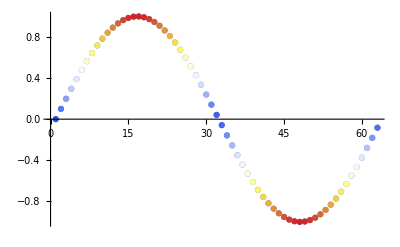

```mathematica
ListPlot@Table[Style[Sin[x],ColorData["TemperatureMap"][Abs@Sin[x]]],{x,0,2π,0.1}]
```

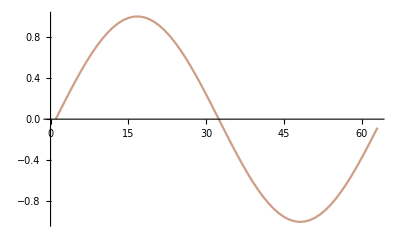

```mathematica
ListLinePlot[Table[Sin[x],{x,0,2π,0.1}],ColorFunctionScaling->False,ColorFunction->(ColorData["TemperatureMap"][Abs@#2]&)]
```